```mathematica
(** simple model for development involving cell divisions and reamplifications **)
```

```mathematica
vhafterk[n0_, nk_,k_]:=1/n0 ((2/(2(nk/n0)^(1/k)))^k-1)/((2/(2(nk/n0)^(1/k)))-1);
```

```mathematica
N[vhafterk[10^5,300,29]]
N[vhafterk[300,5000,7]]
```

0.0149843

0.00946732

```mathematica
v0predict = N[vhafterk[10^5,b,29]+vhafterk[b,5000,7]]
```

(0.00001 (-1.+100000./b))/(-1.+1.48735/b^(1/29))+(-1.+0.0002 b)/((-1.+0.296194/(1/b)^(1/7)) b)

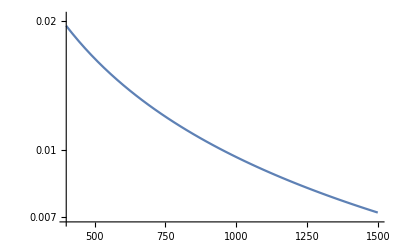

```mathematica
LogPlot[v0predict, {b, 400, 1500}, PlotRange->All]
```

```mathematica
v0predict/.b->2500
v0predict/.b->950
v0predict/.b->550
v0predict/.b->370
```

0.00499653

0.010023

0.0151845

0.0207

```mathematica
(** inverting a function -- to compute dynamics of transformed heteroplasmy (used in Mouse/) **)
```

```mathematica
invgfn[x_]:= 1/(1+Exp[-x])
gfn[y_] :=  Log[-y/(y-1)]
ffn[x_] := PDF[NormalDistribution[μ[t],σ[t]],x]
Ffn[x_]:= CDF[NormalDistribution[μ[t], σ[t]], x]
```

```mathematica
(* F_Y(y) = F_X(g^-1(y)) *)
(*f_Y(y) = f_X(x1)/g'(x1) where g(x1) = y *)
```

```mathematica
gprime = Simplify[D[gfn[x],x]]/.x->μ[t]
g2prime = Simplify[D[gfn[x],{x,2}]]/.x->μ[t]
```

1/(μ[t]-μ[t]^2)

(-1+2 μ[t])/((-1+μ[t])^2 μ[t]^2)

```mathematica
ef = Simplify[gfn[μ[t]] + g2prime/2 σ[t]^2]
vf = Simplify[(gprime)^2 σ[t]^2]
```

Log[-μ[t]/(-1+μ[t])]+((-1+2 μ[t]) σ[t]^2)/(2 (-1+μ[t])^2 μ[t]^2)

σ[t]^2/((-1+μ[t])^2 μ[t]^2)